Barrett Kok protocol when overlap μ is not necessarily 1

The Barrett Kok protocol can establish entanglement between two nodes even in the presence of photon loss or noise. In the protocol, Alice and Bob each entangle their qubit with a photon, and each emit the photon towards a beamsplitter. The experimenter post-selects on detection of one or more photons. Alice and Bob then each apply an X gate to their qubits, entangle with another photon, and again emit towards a beamsplitter. The final entangled state, again post-selecting on detection of one or more photons, will be a fully entangled state shared between Alice and Bob. This notebook plots anticipated fidelity of the final Bell state when the mode overlap μ for the two modes interfering in the beamsplitter during each round is not necessarily 1. 

For information on the Barrett Kok protocol: 
Sean D Barrett and Pieter Kok. 2005. Efficient high-fidelity quantum
computation using matter qubits and linear optics. Physical Review A
71, 6 (2005), 060310.

Initial state:
|e e> |11> + |e↑> |10> + |↑e> |01> + |↑↑> |00>

Matrix element order:
↑↑00
↑↑10
↑↑01
↑↑11
↑e00
↑e10
↑e01
↑e11
e↑00
e↑10
e↑01
e↑11
ee00
ee10
ee01
ee11

The matrix element order for the Kraus and POVM operators follows https://arxiv.org/pdf/1903.09778.pdf page 44:
00
10
01
11
where 0 (1) indicates no detection (detection of photon).

Here I assume the same mode overlap μ on both round 1 and round 2.

```mathematica
fullstate =(1/2) {{1, 0, 0, 0, 0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 1}};
ρ = ConjugateTranspose[fullstate].fullstate
```

{{1/4,0,0,0,0,0,1/4,0,0,1/4,0,0,0,0,0,1/4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,0,0,0,0,0,1/4,0,0,1/4,0,0,0,0,0,1/4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,0,0,0,0,0,1/4,0,0,1/4,0,0,0,0,0,1/4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,0,0,0,0,0,1/4,0,0,1/4,0,0,0,0,0,1/4}}

```mathematica
kraus10 =KroneckerProduct[IdentityMatrix[4],(1/2) {{0, 0, 0, 0}, {0, a1, a2, 0}, {0, a2, a1, 0}, {0, 0, 0, a3}}];
```

```mathematica
kraus01 =KroneckerProduct[IdentityMatrix[4], (1/2) {{0, 0, 0, 0}, {0, a1, a4, 0}, {0, a4, a1, 0}, {0, 0, 0, a3}}];
```

```mathematica
kraus11 = KroneckerProduct[IdentityMatrix[4], (1/Sqrt[2]) {{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, Sqrt[1-Abs[μ]^2]}}];
```

```mathematica
m00 = KroneckerProduct[IdentityMatrix[4], {{1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}];
m10 =  KroneckerProduct[IdentityMatrix[4], (1/2) {{0, 0, 0, 0}, {0, 1, μ, 0}, {0, Conjugate[μ], 1, 0}, {0, 0, 0, (1+Abs[μ]^2)/2}}];
```

```mathematica
m01 =  KroneckerProduct[IdentityMatrix[4], (1/2) {{0, 0, 0, 0}, {0, 1, -μ, 0}, {0, -Conjugate[μ], 1, 0}, {0, 0, 0, (1+Abs[μ]^2)/2}}];
```

```mathematica
m11 = KroneckerProduct[IdentityMatrix[4], (1/2) {{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1-Abs[μ]^2}}];
```

```mathematica
XX = {{0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}};
```

```mathematica
refrho ={{0,0,0,0},{0,1/2,1/2,0},{0,1/2,1/2,0},{0,0,0,0}};
```

```mathematica
Clear[ρ2,ρ3, fullρ3,ρ4,KroneckerList,dof4one, dof4zero, dof3one, dof3zero,partialtraceresult,partialtraceresult2,Zeroes, rho]
calculateRho[m1_, k1_, m2_, k2_]:=
Module[{},
(*Probability of measurement m1 on round 1*)
p1 = Tr[ρ.m1];
ρ2 = FullSimplify[(1/p1)*(k1.ρ.ConjugateTranspose[k1])];
dof4one = KroneckerProduct[ IdentityMatrix[2], IdentityMatrix[2],IdentityMatrix[2],{{0, 1}}];
dof4zero = KroneckerProduct[ IdentityMatrix[2], IdentityMatrix[2],IdentityMatrix[2],{{1, 0}}]; 
dof3one = KroneckerProduct[IdentityMatrix[2], IdentityMatrix[2],{{0, 1}}]; 
dof3zero = KroneckerProduct[IdentityMatrix[2], IdentityMatrix[2], {{1, 0}}]; 
partialtraceresult = dof4one.ρ2.ConjugateTranspose[dof4one]+ dof4zero.ρ2.ConjugateTranspose[dof4zero];
partialtraceresult = dof3one.partialtraceresult.ConjugateTranspose[dof3one]+ dof3zero.partialtraceresult.ConjugateTranspose[dof3zero];
ρ3 = XX.partialtraceresult.ConjugateTranspose[XX];
Zeroes = {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
KroneckerList = Table[KroneckerProduct[ReplacePart[Zeroes, {i,j}->ρ3[[i, j]]], ReplacePart[Zeroes, {i,j}->1]] , {i, 4}, {j, 4}] ;
fullρ3 = Fold[Plus, 0, Fold[Plus, 0, KroneckerList]];
(*Probability of measurement m1 on round 1*)
p2 = Tr[fullρ3.m2];
ρ4 =  FullSimplify[(1/p2)*(k2.fullρ3.ConjugateTranspose[k2] )]/.{a1-> (Sqrt[1+ μ]+Sqrt[1- μ] )/Sqrt[2], a2-> (Sqrt[1+ μ]-Sqrt[1- μ] )/Sqrt[2],a4-> (Sqrt[1- μ]-Sqrt[1+ μ] )/Sqrt[2], a3-> Sqrt[1 + Abs[μ]^2]};
ρ4 = FullSimplify[ρ4, Assumptions-> μ > 0];
partialtraceresult2 = dof4one.ρ4.ConjugateTranspose[dof4one]+ dof4zero.ρ4.ConjugateTranspose[dof4zero];
rho = FullSimplify[dof3one.partialtraceresult2.ConjugateTranspose[dof3one]+ dof3zero.partialtraceresult2.ConjugateTranspose[dof3zero]];
If[m1 != m2, rho = KroneckerProduct[IdentityMatrix[2], {{1, 0},{0, -1}}].rho. KroneckerProduct[IdentityMatrix[2], {{1, 0},{0, -1}}],rho=rho]]
```

```mathematica
calculateFidelityAndProbability[rho_]:=
Module[{},
fidelity=Tr[MatrixPower[MatrixPower[rho, 1/2].refrho.MatrixPower[rho, 1/2], 1/2]]^2;
result = {p1*p2, fidelity}/.{a1-> (Sqrt[1+ μ]+Sqrt[1- μ] )/Sqrt[2], a2-> (Sqrt[1+ μ]-Sqrt[1- μ] )/Sqrt[2],a4-> (Sqrt[1- μ]-Sqrt[1+ μ] )/Sqrt[2], a3-> Sqrt[1 + Abs[μ]^2]}]
```

```mathematica
testρ4 = calculateFidelityAndProbability[calculateRho[m10, kraus10, m01, kraus01]/.μ->1/.μ->1]/.μ->1/.μ->1
```

{1/8,1}

Expected Fidelity = ∑_(a=(01, 10, 11)) ∑_(b=(01, 10, 11)) Fidelity(a, b)*(Probability(a, b))/(∑_Probabilities)

```mathematica
mList = {m01, m10, m11};
kList = {kraus01, kraus10, kraus11};
```

```mathematica
Table[calculateFidelityAndProbability[calculateRho[mList[[ii]],kList[[ii]], mList[[ jj]], kList[[jj]]]/.μ->1], {ii, 2}, {jj, 2}]/.μ->1
```

{{{1/8,1},{1/8,1}},{{1/8,1},{1/8,1}}}

General case where μ !=1

```mathematica
mu = 0.9; 
tab = Table[calculateFidelityAndProbability[calculateRho[mList[[ii]],kList[[ii]], mList[[ jj]], kList[[jj]]]/.μ->mu], {ii, 2}, {jj, 2}]/.μ->mu
```

{{{0.125,0.905},{0.125,0.905}},{{0.125,0.905},{0.125,0.905}}}

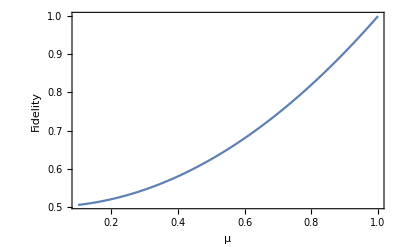

```mathematica
(*Fidelity vs mu, mode overlap*)
Plot[calculateFidelityAndProbability[calculateRho[mList[[1]],kList[[1]], mList[[ 1]], kList[[1]]]][[2]], {μ, 0.1, 1}, FrameLabel->{"μ", "Fidelity"}, Frame->True, LabelStyle->{FontSize->14}]
```